```mathematica
NA = 6.0221367 10^23;
Dtot=10^-12;
kd=10^3;
sigma=1 10^-8;
kf=10 * sigma * Dtot;
kD=4*Pi*sigma*Dtot;
h=(1+kf/kD)*Sqrt[Dtot]/sigma;
a=kd*Sqrt[Dtot]/sigma;
r0=sigma;
tau = sigma^2 / Dtot;
t= tau 10^2;
maxr = 4.5 Sqrt[ 6 Dtot t];
```

```mathematica
ciccio=N[Solve[{x+y+z==h, x*y+y*z+x*z==kd,x*y*z==a},{x,y,z}]];
alpha=ciccio[[1,1,2]];
beta = ciccio[[1,2,2]];
gamma=ciccio[[1,3,2]];
```

```mathematica
W[x_,y_]:=Exp[2*x*y+y^2]*Erfc[x+y];
frac[x_,y_,z_]:=(x*(z+x)*(x+y))/((z-x)*(x-y));
coeff[r_]:=1/(4*Pi*r*r0*Sqrt[Dtot]);
term1[r_]:=1/Sqrt[4*Pi*t]*(Exp[-(r-r0)^2/(4*Dtot*t)]+Exp[-(r+r0-2*sigma)^2/(4*Dtot*t)]);
term2[r_]:=frac[alpha,beta,gamma]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),alpha*Sqrt[t]];
term3[r_]:=frac[beta,gamma,alpha]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),beta*Sqrt[t]];
term4[r_]:=frac[gamma,alpha,beta]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),gamma*Sqrt[t]];
```

```mathematica
f[r_]:=4*Pi*r^2*Re[coeff[r]*(term1[r]+term2[r]+term3[r]+term4[r])]
```

c = N[Integrate[f[r], {r, 1, Infinity}]]

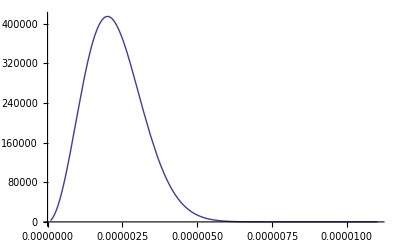

```mathematica
Plot[f[r], {r,sigma,maxr}]
```

```mathematica
out=Table[{r,f[r]},{r,sigma,maxr,(maxr - sigma) / 100}] // N
```

{{1.×10^-7,2786.1},{2.09227×10^-7,12118.5},{3.18454×10^-7,27692.3},{4.27681×10^-7,48959.9},{5.36908×10^-7,75179.9},{6.46135×10^-7,105449.},{7.55362×10^-7,138742.},{8.64589×10^-7,173950.},{9.73816×10^-7,209934.},{1.08304×10^-6,245560.},{1.19227×10^-6,279749.},{1.3015×10^-6,311513.},{1.41072×10^-6,339986.},{1.51995×10^-6,364452.},{1.62918×10^-6,384361.},{1.73841×10^-6,399341.},{1.84763×10^-6,409195.},{1.95686×10^-6,413898.},{2.06609×10^-6,413584.},{2.17531×10^-6,408528.},{2.28454×10^-6,399120.},{2.39377×10^-6,385848.},{2.50299×10^-6,369263.},{2.61222×10^-6,349960.},{2.72145×10^-6,328547.},{2.83068×10^-6,305629.},{2.9399×10^-6,281783.},{3.04913×10^-6,257545.},{3.15836×10^-6,233395.},{3.26758×10^-6,209754.},{3.37681×10^-6,186971.},{3.48604×10^-6,165328.},{3.59527×10^-6,145038.},{3.70449×10^-6,126251.},{3.81372×10^-6,109055.},{3.92295×10^-6,93489.9},{4.03217×10^-6,79547.3},{4.1414×10^-6,67184.},{4.25063×10^-6,56327.2},{4.35985×10^-6,46882.8},{4.46908×10^-6,38741.9},{4.57831×10^-6,31786.7},{4.68754×10^-6,25896.},{4.79676×10^-6,20949.1},{4.90599×10^-6,16829.2},{5.01522×10^-6,13426.},{5.12444×10^-6,10637.4},{5.23367×10^-6,8370.36},{5.3429×10^-6,6541.72},{5.45212×10^-6,5078.},{5.56135×10^-6,3915.27},{5.67058×10^-6,2998.55},{5.77981×10^-6,2281.15},{5.88903×10^-6,1723.87},{5.99826×10^-6,1294.11},{6.10749×10^-6,965.083},{6.21671×10^-6,714.985},{6.32594×10^-6,526.232},{6.43517×10^-6,384.782},{6.5444×10^-6,279.523},{6.65362×10^-6,201.741},{6.76285×10^-6,144.661},{6.87208×10^-6,103.062},{6.9813×10^-6,72.9529},{7.09053×10^-6,51.3085},{7.19976×10^-6,35.8546},{7.30898×10^-6,24.8952},{7.41821×10^-6,17.1755},{7.52744×10^-6,11.7741},{7.63667×10^-6,8.02013},{7.74589×10^-6,5.4284},{7.85512×10^-6,3.65094},{7.96435×10^-6,2.43997},{8.07357×10^-6,1.62038},{8.1828×10^-6,1.06931},{8.29203×10^-6,0.701217},{8.40125×10^-6,0.456946},{8.51048×10^-6,0.295901},{8.61971×10^-6,0.190414},{8.72894×10^-6,0.121767},{8.83816×10^-6,0.0773812},{8.94739×10^-6,0.0488681},{9.05662×10^-6,0.030669},{9.16584×10^-6,0.0191278},{9.27507×10^-6,0.0118555},{9.3843×10^-6,0.00730245},{9.49353×10^-6,0.00447008},{9.60275×10^-6,0.00271933},{9.71198×10^-6,0.00164403},{9.82121×10^-6,0.000987788},{9.93043×10^-6,0.000589827},{0.0000100397,0.000350021},{0.0000101489,0.000206432},{0.0000102581,0.000120996},{0.0000103673,0.000070483},{0.0000104766,0.0000408051},{0.0000105858,0.0000234782},{0.000010695,0.0000134257},{0.0000108042,7.63012×10^-6},{0.0000109135,4.30976×10^-6},{0.0000110227,2.41936×10^-6}}

```mathematica
Export["p_rev.2.tsv",out]
```

p_rev.2.tsv